```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{10,500,50,1,100000,200}];
Subscript[R, lqr]=DiagonalMatrix[{1,300}];
Subscript[L, 0]=0.15;Subscript[Q, 0]=90;
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*====================求解等效腿的质量分布====================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
(*θ=(Subscript[Q, 0]-90)/180*Pi;*)
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr]
```

{{1.89031,15.0355,78.4889,10.3368,250.04,8.76237},{-0.146364,-1.18306,-13.2436,-1.57301,11.6865,1.90347}}

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{1,1200,50,1,12000,1}];
Subscript[R, lqr]=DiagonalMatrix[{2,10}];
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*限位*)
upLimit=-23.41;(*上限位*)
downLimit=67.89;(*下限位*)
(*电机半径--画图*)
Subscript[R, jm]=0.045;(*GO8010*)
Subscript[R, wm]=0.0675;(*MF9025*)
(*Save[NotebookDirectory[]<>"\\VMCsolution.m",VMCForwardSolution,VMCInverseSolution];*)
Get["VMCsolution.m",Path->NotebookDirectory[]]
SystemCalcu[L0_,Q0_]:=(
Module[{},
Subscript[L, 0]=L0;
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[L0,Q0,{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*====================求解等效腿的质量分布====================*)
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
θ=(Q0-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
Return[Subscript[K, lqr]];
];
);
Manipulate[SystemCalcu[L0,Q0],{{L0,0.2},0.1,0.4},{{Q0,90},180,0}](*显示具体数值*)
```

{0.502847-0.552852 x-1.2615 x^2+2.42235 x^3,17.5762-19.3993 x-43.4934 x^2+83.862 x^3,17.7384+114.278 x-401.373 x^2+405.832 x^3,3.81497+10.311 x-23.7919 x^2+18.8466 x^3,50.9598+97.3049 x-107.003 x^2+8.75984 x^3,0.206739+30.618 x-58.7337 x^2+42.6393 x^3,-0.219241-0.317939 x+0.248377 x^2+0.133513 x^3,-7.7184-10.821 x+7.5241 x^2+5.81422 x^3,-16.705-93.0278 x+49.1845 x^2-4.51065 x^3,-3.7674-1.73196 x-47.5051 x^2+44.3686 x^3,27.8796-42.5648 x-20.992 x^2+78.5961 x^3,6.41871-21.3247 x+41.2166 x^2-33.5027 x^3}

{{0.502847,-0.552852,-1.2615,2.42235},{17.5762,-19.3993,-43.4934,83.862},{17.7384,114.278,-401.373,405.832},{3.81497,10.311,-23.7919,18.8466},{50.9598,97.3049,-107.003,8.75984},{0.206739,30.618,-58.7337,42.6393},{-0.219241,-0.317939,0.248377,0.133513},{-7.7184,-10.821,7.5241,5.81422},{-16.705,-93.0278,49.1845,-4.51065},{-3.7674,-1.73196,-47.5051,44.3686},{27.8796,-42.5648,-20.992,78.5961},{6.41871,-21.3247,41.2166,-33.5027}}

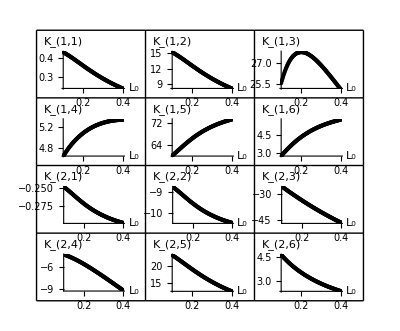

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{1,1200,50,1,12000,1}];
Subscript[R, lqr]=DiagonalMatrix[{2,10}];
Subscript[L, 0]=0.3;Subscript[Q, 0]=90;
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*=============================================系统参数配置=============================================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*=============================================开始循环迭代============================================*)
sampleNum=101;(*循环次数*)
paramNum=12;(*变量个数*)
Kt=Array[0,{sampleNum}];
Lt=Array[0,{sampleNum}];
Do[
(*输入量控制*)
Subscript[L, 0]=0.10+0.3*(cnt)/sampleNum;
Subscript[Q, 0]=90;
(*=========================================求解等效腿的质量分布====================================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*============================================腿部模型参数传递====================================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*============================================导入模型============================================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
α=0;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*============================================LQR控制============================================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
(*============================================数据记录===========================================*)
Kt[[cnt]] = Subscript[K, lqr];
Lt[[cnt]] = Subscript[L, 0];
,{cnt,sampleNum}];
(*============================================多项式拟合============================================*)
(*提取同一参数在不同条件下的值*)
kArray=Array[0,{paramNum}];Do[Do[kArray[[(i-1)*6+j]]=Kt[[All,i,j]],{j,6}],{i,2}];	
(*将条件值与参数值配对*)
Kxy=Array[0,{paramNum,sampleNum}];
Do[Do[Kxy[[i,j]]={Lt[[j]],kArray[[i,j]]},{j,sampleNum}],{i,paramNum}];	
(*分别对各个参数进行多项式拟合*)
Kpoly = Array[0, {paramNum}];
Do[Kpoly[[i]]= Fit[Kxy[[i]],{1,x,x^2,x^3},x],{i,paramNum}];
Kpoly
(*将多项式系数整合成一个矩阵*)
kPolyMatrix = Array[0,{12}];
Do[kPolyMatrix[[i]]=CoefficientList[Kpoly[[i]],x],{i,paramNum}];
(*多项式拟合曲线*)
KT = Array[0, {paramNum}];
Do[KT[[plotcnt]] = Plot[Kpoly[[plotcnt]], {x, Lt[[1]], Lt[[sampleNum]]}, Epilog->Point[Kxy[[plotcnt]]],Axes->{True,True}, AxesLabel->{"L_0", Subscript[K, 1,plotcnt]}],{plotcnt, 1, 6}];
Do[KT[[plotcnt]] = Plot[Kpoly[[plotcnt]], {x, Lt[[1]], Lt[[sampleNum]]}, Epilog->Point[Kxy[[plotcnt]]],Axes->{True,True}, AxesLabel->{"L_0", Subscript[K, 2,plotcnt-6]}],{plotcnt, 7, 12}];
KL0Graph = GraphicsGrid[{{KT [[1]],KT [[2]],KT [[3]]},{KT [[4]],KT [[5]],KT [[6]]},
	{KT [[7]],KT [[8]],KT [[9]]},{KT [[10]],KT [[11]],KT [[12]]}}, Frame->All,ImageSize->Full];
(*============================================数据输出===========================================*)
Print[kPolyMatrix];(*拟合多项式升幂排列*)
Show[KL0Graph](*多项式拟合曲线图*)
```

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{1,1200,50,1,12000,1}];
Subscript[R, lqr]=DiagonalMatrix[{2,10}];
Subscript[L, 0]=0.3;Subscript[Q, 0]=90;
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*=============================================系统参数配置=============================================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*=============================================开始循环迭代============================================*)
sampleNum=51;(*循环次数*)
paramNum=12;(*变量个数*)
Kt=Array[0,{sampleNum,sampleNum}];
Xt=Array[0,{sampleNum,sampleNum}];
Do[
Do[
(*输入量控制*)
Subscript[L, 0]=0.10+0.2*(cnt1)/sampleNum;
Subscript[Q, 0]=40+100*(cnt2)/sampleNum;
(*=========================================求解等效腿的质量分布====================================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*============================================腿部模型参数传递====================================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*============================================导入模型============================================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*============================================LQR控制============================================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
(*============================================数据记录===========================================*)
Kt[[cnt1,cnt2]] = Subscript[K, lqr];
Xt[[cnt1,cnt2]]={Subscript[L, 0],Subscript[Q, 0]};
,{cnt1,sampleNum}];
,{cnt2,sampleNum}];
(*============================================多项式拟合============================================*)
(*提取同一参数在不同条件下的值*)
kArray=Array[0,{paramNum}];Do[Do[kArray[[(i-1)*6+j]]=Kt[[All,All,i,j]],{j,6}],{i,2}];
(*将条件值与参数值配对*)
Kxy=Array[0,{paramNum,sampleNum*sampleNum}];
Do[Do[Do[Kxy[[i,(j-1)*sampleNum+k]]={Xt[[j,k,1]],Xt[[j,k,2]],kArray[[i,j,k]]},{k,sampleNum}],{j,sampleNum}],{i,paramNum}];
(*分别对各个参数进行多项式拟合*)
Kpoly = Array[0, {paramNum}];
Do[Kpoly[[i]]= Fit[Kxy[[i]],{1,x,x^2,x^3,y,y^2,y^3,x*y,x^2*y,x*y^2},{x,y}],{i,paramNum}];
(*将多项式系数整合成一个矩阵*)
kPolyMatrix = Array[0,{12}];
Do[kPolyMatrix[[i]]=CoefficientList[Kpoly[[i]],{x,y}],{i,paramNum}];
(*多项式拟合曲线*)
KT = Array[0, {paramNum}];
KTT=Array[0,{paramNum}];
Do[KT[[plotcnt]] = Plot3D[Kpoly[[plotcnt]], {x, Xt[[1,1,1]], Xt[[sampleNum,sampleNum,1]]},{y, Xt[[1,1,2]], Xt[[sampleNum,sampleNum,2]]},Axes->{True,True,True}, AxesLabel->{"L_0", "Q_0",Subscript[K, 1,plotcnt]}];
KTT[[plotcnt]]=ListPlot3D[Kxy[[plotcnt]]],{plotcnt, 1, 6}];
Do[KT[[plotcnt]] = Plot3D[Kpoly[[plotcnt]],{x, Xt[[1,1,1]], Xt[[sampleNum,sampleNum,1]]},{y, Xt[[1,1,2]], Xt[[sampleNum,sampleNum,2]]}, Axes->{True,True,True}, AxesLabel->{"L_0", "Q_0",Subscript[K, 2,plotcnt-6]}];
KTT[[plotcnt]]=ListPlot3D[Kxy[[plotcnt]]],{plotcnt, 7, 12}];
KL0Graph = GraphicsGrid[{{KT[[1]],KT[[2]],KT[[3]]},{KT[[4]],KT[[5]],KT[[6]]},
	{KT[[7]],KT[[8]],KT[[9]]},{KT[[10]],KT[[11]],KT[[12]]}}, Frame->All,ImageSize->Full];
KLTGraph = GraphicsGrid[{{KT[[1]],KTT[[1]]},{KT[[2]],KTT[[2]]},{KT[[3]],KTT[[3]]},{KT[[4]],KTT[[4]]},{KT[[5]],KTT[[5]]},{KT[[6]],KTT[[6]]},{KT[[7]],KTT[[7]]},{KT[[8]],KTT[[8]]},{KT[[9]],KTT[[9]]},{KT[[10]],KTT[[10]]},{KT[[11]],KTT[[11]]},{KT[[12]],KTT[[12]]}}, Frame->All,ImageSize->Full];
(*============================================数据输出===========================================*)
Print[kPolyMatrix];(*拟合多项式升幂排列*)
Show[KL0Graph]
Show[KLTGraph]
(*多项式拟合曲线图*)
```

{{{0.408186,0.00217609,-0.000015453,2.74332×10^-8},{-0.893694,0.0117528,-0.0000708512,0},{-2.7713,0.00253199,0,0},{5.1657,0,0,0}},{{14.2911,0.0759267,-0.000538724,9.55427×10^-7},{-31.4449,0.406339,-0.00245339,0},{-94.4755,0.0891849,0,0},{176.711,0,0,0}},{{8.32712,0.24364,-0.00194526,4.26337×10^-6},{20.2547,2.35635,-0.0132789,0},{-540.651,0.121233,0,0},{683.937,0,0,0}},{{4.42942,0.00229396,-0.0000680122,4.42172×10^-7},{-5.41233,0.158065,-0.000963529,0},{15.0196,0.0426378,0,0},{-44.7531,0,0,0}},{{62.4361,-0.294243,0.00185985,-1.9696×10^-6},{103.879,0.126096,-0.000152545,0},{-125.504,-0.236896,0,0},{9.57878,0,0,0}},{{-0.569729,-0.000578213,0.0000399471,-3.79235×10^-7},{44.5089,-0.0768302,0.000599624,0},{-105.238,-0.0742438,0,0},{117.765,0,0,0}},{{-0.266832,0.00112324,-7.11821×10^-6,7.3739×10^-9},{-0.294583,-0.000185065,-6.78057×10^-7,0},{0.0114279,0.000744735,0,0},{0.627534,0,0,0}},{{-9.39764,0.0390712,-0.000248464,2.61165×10^-7},{-10.2394,0.00802773,-0.000101943,0},{-2.81769,0.0250758,0,0},{26.3449,0,0,0}},{{-19.1337,0.0149978,0.000481093,-3.76958×10^-6},{21.0896,-2.53753,0.0138707,0},{83.7176,0.0445883,0,0},{-58.9212,0,0,0}},{{-4.2772,-0.0104324,0.0000730083,-1.26439×10^-7},{-15.7937,0.640351,-0.00351586,0},{-118.785,-0.024701,0,0},{157.778,0,0,0}},{{25.249,0.0908948,-0.000697073,1.63505×10^-6},{-87.6934,0.792154,-0.00481768,0},{-8.08296,0.187808,0,0},{76.2196,0,0,0}},{{9.81897,-0.0581698,0.00029942,2.5487×10^-7},{-37.352,0.103956,-0.000705288,0},{96.3104,0.0560473,0,0},{-125.855,0,0,0}}}

-Graphics-

-Graphics-